# Data Science and Machine Learning

## Assignment 2: Prediction, classification, and clustering

In this assignment, we will use a dataset to perform prediction and classification operations:
	First, we will use the same dataset as in Assignment 1, picking up where we left of. Recall that the dataset contains different environmental, social and governance (ESG) scores of 	companies across different years as well a set of features, e.g, market value, assets, etc.
	Second, we will classify images of Sustainable Development Goals (SDGs)
Once you are done you have to submit your notebook here: https://moodle.epfl.ch/mod/assign/view.php?id=1159930 
There is no quiz, so your grade will depend only on your notebook.
If there is need for further clarifications on the questions, after the assignment is released, we will update this file, so make sure you check the git repository for updates.
	Good luck!

Import as a dataset the CSV file: "https://storage.googleapis.com/mgt_492/dataESG.csv"

```mathematica
dataset = Import["https://storage.googleapis.com/mgt_492/dataESG.csv", "Dataset", "HeaderLines" -> 1];
```

## Prediction: ESG Score

Question 1: 
Build a linear regression model for "ESG controversy score" using the following attributes:
"mv", "mc", "tobin", "roe", "oia", "ois", "assets", "roa", "sg", "lev", "div", "ind", "country" [1 point]

```mathematica
regressKeys = { "ESG controversy score", "mv", "mc", "tobin", "roe", "oia", "ois", "assets", "roa", "sg", "lev", "div", "ind", "country"};
```

```mathematica
dataR = dataset[All, regressKeys];
```

```mathematica
pESG = Predict[dataR -> "ESG controversy score", Method -> "LinearRegression"]
```

PredictorFunction[…]

```mathematica
Information[pESG]
```

Predictor information
Data type | Mixed (number: 13)
Standard deviation | 0.293 ± 0.024
Method | LinearRegression
Single evaluation time | 11.6 ms/example
Batch evaluation speed | 3.37 examples/ms
Loss | 0.204 ± 0.079
Model memory | 427. kB
Training examples used | 1007 examples
Training time | 2.08 s
 |

```mathematica
Information[pESG, "Properties"]
```

{AcceptanceThreshold,AnomalyDetector,BatchEvaluationSpeed,BatchEvaluationTime,Calibrated,EvaluationTime,ExampleNumber,FeatureNames,FeatureNumber,FeatureTypes,FunctionMemory,FunctionProperties,IndeterminateThreshold,L1Regularization,L2Regularization,LearningCurve,MaxTrainingMemory,MeanCrossEntropy,Method,MethodDescription,MethodOption,MissingSynthesizer,OptimizationMethod,PerformanceGoal,Properties,StandardDeviation,TrainingLabelMean,TrainingTime,UtilityFunction}

Question 2: 
What is the standard deviation of your predictor? [1 point]

```mathematica
pStandardDeviation =Information[pESG, "StandardDeviation"]
```

0.2930.024

Question 3: 
Create a BarChart of the impact of features on prediction for the company "1&1 DRILLISH" (first company of the dataset)? [1 point]
Hint: You can get an estimation for how much each feature impacted the predictor's output by computing the  SHAP values.

```mathematica
drillish = First[dataR];
```

```mathematica
impacts = pESG[drillish, "SHAPValues"]
```

<|mv→0.00130447,mc→0.00355142,tobin→0.0239199,roe→0.0034519,oia→0.000398287,ois→0.0019818,assets→0.004596,roa→0.00771355,sg→-0.00350708,lev→0.00940394,div→-0.0043482,ind→0.00345137,country→-0.0292586|>

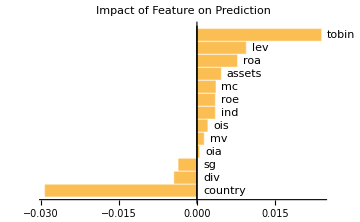

```mathematica
BarChart[Sort[impacts], ChartLabels -> Placed[Automatic, After], 
 ImageSize -> Medium, BarOrigin -> Left, 
 PlotLabel -> "Impact of Feature on Prediction"]
```

Question 4: 
What are the L1 and L2 regularization coefficients of your predictor? [1 point]

```mathematica
penaltyL1 = Information[pESG, "L1Regularization"]
penaltyL2 = Information[pESG, "L2Regularization"]
```

0

100.

Question 5: 
Build another linear regression model for "ESG controversy score" using the same attributes, but with the L1 regularization coefficient equal to 10 and the L2 regularization coefficient equal to 0. [1 point]

```mathematica
pESGL1 = Predict[dataR -> "ESG controversy score", Method -> {"LinearRegression",
"L1Regularization" ->10, 
"L2Regularization" -> 0}]
```

PredictorFunction[…]

```mathematica
Information[pESGL1]
```

Predictor information
Data type | Mixed (number: 13)
Standard deviation | 0.295 ± 0.013
Method | LinearRegression
Single evaluation time | 14. ms/example
Batch evaluation speed | 6.84 examples/ms
Loss | 0.206 ± 0.041
Model memory | 281. kB
Training examples used | 1007 examples
Training time | 1.34 s
 |

Question 6: 
What is the standard deviation of your new predictor ? [1 point]

```mathematica
pStandardDeviation =Information[pESGL1, "StandardDeviation"]
```

0.2950.013

## Numerical Classification: ESG label

The "ESG Label" column labels the companies according to their "ESG controversy score", from 1 (very poor performance) to 5 (very good performance). 
We will try to find the ESG label of a company based on its feature (e.g., financial data, location, industry...)

### Logistic regression

Question 7: 
Build a logistic regression model for "ESG Label" using the following attributes:
"mv", "mc", "tobin", "roe", "oia", "ois", "assets", "roa", "sg", "lev", "div", "ind", "country"
1) Split your dataset into 80% training and 20% test. Randomize your dataset. 
2) Build your classifier. [1 point]

```mathematica
classifyKeys = { "ESG Label", "mv", "mc", "tobin", "roe", "oia", "ois", "assets", "roa", "sg", "lev", "div", "ind", "country"};
```

```mathematica
dataC = dataset[All, classifyKeys];
```

```mathematica
{nobs,ncol}=Dimensions[dataC];
```

```mathematica
{trainingset,testset}=TakeDrop[dataC,Floor[nobs*0.8]];
```

```mathematica
cESG = Classify[trainingset-> "ESG Label", Method -> "LogisticRegression"]
```

ClassifierFunction[…]

```mathematica
Information[cESG]
```

Classifier information
Data type | Mixed (number: 13)
Classes | ,,12345
Accuracy | (43.6.) %
Method | LogisticRegression
Single evaluation time | 9.15 ms/example
Batch evaluation speed | 7.19 examples/ms
Loss | 1.52 ± 0.085
Model memory | 368. kB
Training examples used | 805 examples
Training time | 1.6 s
 |

Question 8: 
What is the accuracy on the training set? [1 point]

Information will return the estimated accuracy of the classifier:

```mathematica
Information[cESG, "Accuracy"]
```

0.430.06

You can also use ClassifierMeasurements to obtain the true accuracy computed on the training set.

```mathematica
ClassifierMeasurements[cESG,trainingset,"Accuracy"]
```

0.439752

Both methods were counted as correct for this assignment.

Question 9: 
What is the accuracy on the testing set? [1 point]

```mathematica
cmESG = ClassifierMeasurements[cESG,testset]
```

Classifier Measurements
Classifier method | LogisticRegression
Number of test examples | 202
Accuracy | (42.63.5) %
Accuracy baseline | (21.82.9) %
Geometric mean of probabilities | 0.247 ± 0.014
Mean cross entropy | 1.4 ± 0.056
Single evaluation time | 9.9 ms/example
Batch evaluation speed | 3.95 examples/ms
-Graphics- |

```mathematica
cmESG["Accuracy"]
```

0.425743

### Decision Tree

Question 10: 
Using the same training/testing set and features as before, build a Decision Tree Classifier for "ESG Label". [1 point]

```mathematica
cESGtree = Classify[trainingset-> "ESG Label", Method -> "DecisionTree"]
```

ClassifierFunction[…]

Question 11: 
What is the accuracy on the training set? [0.5 point]
What is the accuracy on the testing set? [0.5 point]

```mathematica
Information[cESGtree, "Accuracy"]
```

0.1740.031

```mathematica
ClassifierMeasurements[cESGtree,testset, "Accuracy"]
```

0.148515

It is important to always check the confusion matrix. Here, our classifier performs extremely poorly to identify class 3...
The accuracy is actually even lower than the baseline.

```mathematica
ClassifierMeasurements[cESGtree,testset, "ConfusionMatrixPlot"]
```

-Graphics-

Evaluate the tree depth influence on the Decision Tree Classifier testing accuracy by varying the number of feature used from 1 to 10.

We first create a function with argument the fraction of feature that returns a (trained) classifier:

```mathematica
cESGtreedepth[f_] := Classify[trainingset-> "ESG Label", Method -> {"DecisionTree", "FeatureFraction" -> f}];
```

Now we compute the accuracy on the testing set, first mapping our classifier function on the number of features (converting the actual number of features into a fraction), then applying ClassifierMeasurements:

```mathematica
cmESGtreeAccu =ClassifierMeasurements[cESGtreedepth[#],testset, "Accuracy"] &/@ (Range[10]/(ncol-1));
```

We create an association between our number of features and testing set accuracy:

```mathematica
cmESGtreebestdepth =AssociationThread[Range[10] -> cmESGtreeAccu ]
```

<|1→0.311881,2→0.341584,3→0.415842,4→0.361386,5→0.371287,6→0.405941,7→0.371287,8→0.361386,9→0.420792,10→0.405941|>

Question 12: 
What number of features gives the best testing accuracy? [1 point]

```mathematica
TakeLargest[cmESGtreebestdepth,1]
```

<|9→0.420792|>

By manually modifying the number of features, we got a better accuracy than with the default classifier.
Indeed, the default classifier is not only optimizing the accuracy, but also the training time for instance. It also cannot check all the configurations of parameters...
It is thus good practice to explore what is happening when you modify the parameters of your model.

### Nearest Neighbors

Question 13: 
Using the same training/testing set and features as before, build a kNN Classifier for "ESG Label".  [1 point]

```mathematica
cESGkNN = Classify[trainingset-> "ESG Label", Method -> "NearestNeighbors"]
```

ClassifierFunction[…]

Question 14: 
What is the accuracy on the training set? [0.5 point]
What is the accuracy on the testing set? [0.5 point]

```mathematica
Information[cESGkNN, "Accuracy"]
```

0.3960.027

```mathematica
ClassifierMeasurements[cESGkNN,testset, "Accuracy"]
```

0.40099

```mathematica
ClassifierMeasurements[cESGkNN,testset, "ConfusionMatrixPlot"]
```

-Graphics-

Using the same training/testing set as before, evaluate the influence of the number of neighbors on the kNN Classifier testing accuracy by varying the number of neihbors used from 1 to 10.

We first create a function with argument the number of neighbors that returns a (trained) classifier:

```mathematica
cESGkNNsearch[k_] := Classify[trainingset-> "ESG Label", Method -> {"NearestNeighbors", "NeighborsNumber" ->k}];
```

We compute the accuracy on the testing set, first mapping our classifier function on the number of neighbors, then applying ClassifierMeasurements:

```mathematica
cmESGkNNaccu =ClassifierMeasurements[cESGkNNsearch[#],testset, "Accuracy"] &/@ Range[10];
```

Finally, we create an association between the number of neighbors and the computed testing set accuracy:

```mathematica
cmESGkNNbestk =AssociationThread[Range[10] -> cmESGkNNaccu ]
```

<|1→0.405941,2→0.371287,3→0.391089,4→0.440594,5→0.435644,6→0.475248,7→0.465347,8→0.415842,9→0.430693,10→0.440594|>

Question 15: 
What number of neighbors gives the best testing accuracy? [1 point]

```mathematica
TakeLargest[cmESGkNNbestk,1]
```

<|6→0.475248|>

As before, we obtain a better accuracy.

## Image classification: Sustainable Development Goals

The Sustainable Development Goals are a collection of 17 global goals to transition towards a more sustainable future.
We will try to classify images of the SDGs icons.

First, import a list of 10 thumbnails of the 17 SDGs from a web image search. As search query, you can use the following:
"SDG 1", "SDG 2", "SDG 3", "SDG 4", "SDG 5", "SDG 6", "SDG 7", "SDG 8", "SDG 9", "SDG 10", "SDG 11", "SDG 12", "SDG 13", "SDG 14", "SDG 15", "SDG 16", "SDG 17"

Alternatively, you can import the images from the PDF file "ImagesSDG.pdf" with the following line of code (replace folder with the path to your file):
	sdgImages = Partition[ImageReflect /@ Flatten @ Values @ Import["folder/ImagesSDG.pdf", "EmbeddedImages"],10];

```mathematica
sdgClasses = {"SDG 1", "SDG 2", "SDG 3", "SDG 4", "SDG 5", "SDG 6", "SDG 7", "SDG 8", "SDG 9", "SDG 10", "SDG 11", "SDG 12", "SDG 13", "SDG 14", "SDG 15", "SDG 16", "SDG 17"};
```

Method 1: WebImageSearch

```mathematica
WebImageSearch[#,"Thumbnails",MaxItems->10] & /@sdgClasses;
```

Method 2: Extract from PDF:

```mathematica
sdgImages = Partition[ImageReflect /@ Flatten @ Values @ Import["MGT-492/Assignment/Assignment 2/ImagesSDG.pdf", "EmbeddedImages"],10];
```

```mathematica
sdgImages[[15,{3,9}]]
```

{-Graphics-,-Graphics-}

Then, associate each image to its label ("SDG 1", "SDG 2", "SDG 3", "SDG 4", "SDG 5", "SDG 6", "SDG 7", "SDG 8", "SDG 9", "SDG 10", "SDG 11", "SDG 12", "SDG 13", "SDG 14", "SDG 15", "SDG 16", "SDG 17")

```mathematica
sdgDataset=Flatten[Thread/@Thread[sdgImages->sdgClasses]];
```

Question 16: 
Build a classifier model that return the SDG goal (e.g. "SDG 1") using images as input.
Split your dataset into 80% training and 20% test. Do not forget to randomize your dataset. [1 point]

```mathematica
sdgNobs = Length[sdgDataset];
```

```mathematica
{sdgTrainingset,sdgTestset}=TakeDrop[RandomSample[sdgDataset],Floor[sdgNobs*0.8]];
```

```mathematica
cSDG = Classify[sdgTrainingset]
```

ClassifierFunction[…]

Question 17: 
What is the accuracy on the training set? [0.5 point]
What is the accuracy on the testing set? [0.5 point]

```mathematica
Information[cSDG, "Accuracy"]
```

0.590.05

```mathematica
ClassifierMeasurements[cSDG,sdgTrainingset, "Accuracy"]
```

0.955882

```mathematica
cmSDG = ClassifierMeasurements[cSDG,sdgTestset];
cmSDG["Accuracy"]
cmSDG["ConfusionMatrixPlot"]
```

0.382353

-Graphics-

Question 18: 
Find the 3 worst classified images of the testing set. [0.5 point]
For each of these examples, find the 2 most likely classes according to your classifier? [0.5 point]

```mathematica
misClassSDG = cmSDG["WorstClassifiedExamples"->3]
```

{-Graphics-→SDG 14,-Graphics-→SDG 3,-Graphics-→SDG 4}

```mathematica
cSDG[misClassSDG[[1,1]], "TopProbabilities"->2]
cSDG[misClassSDG[[2,1]], "TopProbabilities"->2]
cSDG[misClassSDG[[3,1]], "TopProbabilities"->2]
```

{SDG 3→0.999822,SDG 1→0.000153373}

{SDG 14→0.943121,SDG 10→0.0546627}

{SDG 10→0.830944,SDG 14→0.164977}

### Image classifier with dimensionality reduction

Instead of directly working with images, we will try to first perform some dimensionality reduction operation:

Let's project our images on a space of dimensions 17, i.e. our images are converted into vector of 17 elements:

```mathematica
drSDG = DimensionReduction[Flatten @ sdgImages,17];
sdgImagesReduced = drSDG[Flatten @ sdgImages];
```

```mathematica
sdgImagesReduced[[1]]
```

{-7.90762,6.47302,-2.22129,6.2853,0.519891,2.54406,1.5422,0.245923,1.92889,2.01481,-3.13451,-2.34738,-1.40645,3.73941,-2.13943,2.87142,1.49274}

We then prepare our dataset, training set, & testing set:

```mathematica
sdgImagesReducedP = Partition[sdgImagesReduced,10];
sdgDatasetReduced = Flatten[Thread/@Thread[sdgImagesReducedP->sdgClasses]];
```

```mathematica
{sdgTrainingsetReduced,sdgTestsetReduced}=TakeDrop[RandomSample[sdgDatasetReduced],Floor[sdgNobs*0.8]];
```

We train our classifier on the reduced data:

```mathematica
cSDGreduced = Classify[sdgTrainingsetReduced]
```

ClassifierFunction[…]

Let's compute the various accuracy metrics and confusion matrix:

```mathematica
Information[cSDGreduced, "Accuracy"]
```

0.640.13

```mathematica
ClassifierMeasurements[cSDGreduced,sdgTrainingsetReduced, "Accuracy"]
```

0.882353

```mathematica
ClassifierMeasurements[cSDGreduced,sdgTestsetReduced, "Accuracy"]
```

0.470588

```mathematica
ClassifierMeasurements[cSDGreduced,sdgTestsetReduced, "ConfusionMatrixPlot"]
```

-Graphics-

It is possible to obtain better results, with a lower computation time, although there is a tradeoff because the dimensionality reduction task is time expensive). 
However, since our dataset only has 10 images per class, our results are very sensitive to the choice of training/testing set.